```mathematica
(*The population of a country increases at the rate proportional to the number inhabitants. if the population double in 30 years in how many years will it triple *)
```

```mathematica
Clear[P,p0,k,t]
DS= DSolve[{p'[t]==k*p[t],p[0]==p0},p[t],t]
```

{{p[t]→ⅇ^(k t) p0}}

```mathematica
P[t_]=DS[[1,1,2]];
kv = Solve[P[30]==2*p0,k,Reals]
```

{{k→Log[2]/30}}

```mathematica
k = kv[[1,1,2]];
NSolve[P[t]==3*p0,t,Reals]
```

{{t→47.5489}}

```mathematica
(*The differential equation dp/dt==(k Cos[t]) p, where k is positive constant, is a model for a population p[t] that undergoes yearly seasonal flunctuations. Solve the equation subject to p[0]==p0. Use a graphing utility to obtain the graph of the solution for different choices of p0*)
```

```mathematica
DS= DSolve[{p'[t]==(k*Cos[t])*p[t],p[0]==p0},p[t],t]
```

{{p[t]→ⅇ^(k Sin[t]) p0}}

```mathematica
y1[t_]=DS[[1,1,2]];
m1=p0+p0*0.1
```

1.1 p0

```mathematica
m2 = Solve[y1[1]==m1,k]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{k→0.113266}}

```mathematica
y2[t_]=y1[t]/.k->m2[[1,1,2]]
```

ⅇ^(0.113266 Sin[t]) p0

```mathematica
y3[t_]=y2[t]/.p0->100
y4[t_]=y2[t]/.p0->500
y5[t_]=y2[t]/.p0->1000
```

100 ⅇ^(0.113266 Sin[t])

500 ⅇ^(0.113266 Sin[t])

1000 ⅇ^(0.113266 Sin[t])

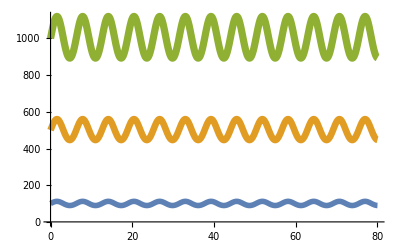

```mathematica
Plot[{y3[t],y4[t],y5[t]},{t,0,80},PlotStyle->{Thickness[0.01],Thickness[0.012],Thickness[0.013]}]
```